# Modelización Matemática - Tema 3

## Diego Ángel Gallardo Costilla

```mathematica
Clear[x,t,a,r,y,e,q]
```

## Ejercicio 3.1

Mediante la función DSolve, resolvemos la ecuación en función de a, b y .

```mathematica
DSolve[{x'[t]==a x[t]-b x[t],x[0]==x0}]
```

{{x[t]→ⅇ^(a t-b t) x0}}

## Ejercicio 3.2

Evaluamos nuestra ecuación diferencial de variable temporal t y concentración de pobla.08ción x(t) dentro de un Plot, con argumentos PlotRange, PlotLabel y AxesLabel para embellecerlo un poco. Mediante la función Manipulate, podemos modificar ambos parámetros a y b, como el valor inicial del PVI para t = 0. Se observa entonces que, si a < b, la población decrece y se extingue; si a = b, será valor constante , y si a > b la población crece hasta diverger.

```mathematica
Manipulate[Plot[Evaluate[x[t]/. DSolve[{x'[t]==a x[t]-b x[t],x[0]==x0}]],{t,0,10},PlotRange->{0,10},PlotLabel->Row[{"Solución para a = ", a, " y b = ", b}],AxesLabel->{"t","x(t)"},Filling->Axis],

{{a,1,"a"},0,5,Appearance->"Labeled"},{{b,0.5,"b"},0,5,Appearance->"Labeled"},{{x0,1,"x0"},0,10,Appearance->"Labeled"}]
```

## Ejercicio 3.3

Primero, defino la función de crecimiento del modelo logístico. Para hallar su punto de máximo crecimiento, la derivo y hallo dónde se anula.

```mathematica
(*Definimos valores para los parámetros*)
r=0.5;
K=100;
F[x_]:=r*x*(1-x/K);
Solve[D[F[x,a,k],x] == 0]
```

{{F^(1,0,0)[x,a,k]→0}}

```mathematica
Manipulate[Plot[F[x,a,K],{x,0,K},PlotRange->{0,5},PlotLabel->Row[{"Modelo Logístico: a = ",a,", K = ",K}],AxesLabel->{"x","f(x)"}],

{{a,1,"Tasa de crecimiento (a)"},0.1,5},{{K,10,"Soporte del entorno (K)"},1,20}]
```

Podemos ver que si la población está entre 0 y K, la tasa es positiva (la población crece), y si supera K, la tasa es negativa (la población decrece)

```mathematica
r=0.5; 
K = 100;
```

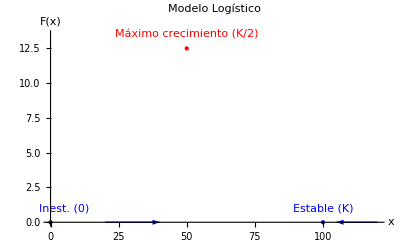

```mathematica
Plot[F[x,r,K],{x,0,120},PlotStyle->Blue,AxesLabel->{"x","F(x)"},PlotLabel->"Modelo Logístico",Epilog->{
(*Punto de máximo crecimiento en K/2*)PointSize[Large],Red,Point[{K/2,F[K/2]}],Text["Máximo crecimiento (K/2)",{K/2,F[K/2]+1}],
(*Señalamos los equilibrios*)PointSize[Medium],Blue,Point[{0,0}],Text["Inest. (0)",{5,1}],Point[{K,0}],Text["Estable (K)",{K,1}],(*Flechas de comportamiento en el eje x*)Arrow[{{20,0},{40,0}}],(*Crece hacia K*)Arrow[{{120,0},{105,0}}] (*Decrece hacia K*)}]
```

## Ejercicio 3.4

Al resolver la ecuación por variables separadas, obtenemos la función logística:

```mathematica
(*Definimos la solución analítica*)
solucionLogistica[t_,a_,K_,x0_]:=(K*x0*Exp[a*t])/(K+x0*(Exp[a*t]-1))

Manipulate[Plot[solucionLogistica[t,a,K,x0],{t,0,20},PlotRange->{0,K*1.1},PlotStyle->{Thick,Blue},AxesLabel->{"t","x(t)"},PlotLabel->Style["Curva Sigmoide Logística",Bold,14],Filling->Axis],

{{a,0.5,"Tasa de reproducción (a)"},0.1,2,Appearance->"Labeled"},{{K,50,"Soporte del medio (K)"},10,100,Appearance->"Labeled"},{{x0,2,"Población inicial (x0)"},0.1,20,Appearance->"Labeled"}]
```

## Ejercicio 3.5

### Modelo Compensatorio

Puntos de equilibrio: Tiene dos puntos de equilibrio:  y .
Estabilidad: El punto  es inestable, mientras que  es asintóticamente estable.
Forma de la curva: Es cualitativamente similar al modelo logístico. La población siempre tiende al valor estable  siempre que la población inicial sea mayor que cero ().

### Modelo Despensatorio

Puntos de equilibrio: Al igual que el compensatorio, tiene dos puntos de equilibrio ( inestable y  estable).
Forma de la curva (Efecto Allee): Su diferencia matemática principal es que la curva de crecimiento es convexa para valores pequeños de población.
Esto indica un crecimiento muy lento al principio hasta alcanzar un punto de inflexión, a partir del cual la curva se vuelve cóncava y el crecimiento es más rápido.
Comportamiento: Aunque el crecimiento inicial es lento, la población sigue tendiendo a estabilizarse en .

### Modelo Despensatorio Crítico

Puntos de equilibrio: Presenta tres puntos de equilibrio: ,  y .
Estabilidad: A diferencia de los anteriores,  es asintóticamente estable.
El punto intermedio  es inestable y el punto superior  es asintóticamente estable.
Tasa de crecimiento: Para concentraciones pequeñas de población, la tasa de crecimiento es negativa (la mortalidad supera a la reproducción).
Umbral de extinción: El punto inestable  actúa como un umbral crítico; si la población inicial  es inferior a , la especie se extingue inevitablemente. Si es superior, se estabiliza en .

## Ejercicio 3.6

### Modelo Compensatorio

He usado una versión sencilla del modelo logístico:

```mathematica
r=0.5;K=10;
Fcomp[x_]:=r*x*(1-x/K);

(*Puntos de equilibrio*)
equilibriosComp=Solve[Fcomp[x]==0,x]

(*Estabilidad:evaluamos la derivada en los equilibrios*)
derComp=D[Fcomp[x],x];
derComp/. equilibriosComp
(*Resultado:F'(0)=0.5>0 (inestable),F'(10)=-0.5<0 (estable)*)
```

{{x→0},{x→10}}

{0.5,-0.5}

### Modelo Despensatorio

En este caso, la función debe ser convexa cerca del origen para reflejar el crecimiento lento (Efecto Allee). He utilizado un término de tipo Hill

{{x→0},{x→0},{x→10}}

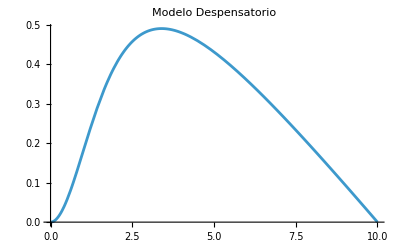

```mathematica
(*Modelo con crecimiento inicial lento*)
Fdesp[x_]:=(x^2/(2^2+x^2))*(1-x/10);

(*Puntos de equilibrio positivos*)
equilibriosDesp=Solve[Fdesp[x]==0&&x>=0,x]

(*Representación para ver la convexidad inicial*)
Plot[Fdesp[x],{x,0,10},PlotLabel->"Modelo Despensatorio"]
```

### Modelo Despensatorio Crítico

Este modelo es el más complejo porque la tasa de crecimiento es negativa para poblaciones muy pequeñas. He definido un polinomio que cruza el eje en un umbral de extinción .

```mathematica
(*Parámetros:r=0.1,umbral a=2,soporte K=10*)
r=0.1;a=2;K=10;
Fcrit[x_]:=r*x*(x/a-1)*(1-x/K);

(*Puntos de equilibrio*)
equilibriosCrit=Solve[Fcrit[x]==0,x]

(*Estabilidad*)
derCrit=D[Fcrit[x],x];
derCrit/. equilibriosCrit
(*Resultados:F'(0)=-0.1<0 (Estable:tendencia a la extinción) F'(2)=0.08>0 (Inestable:umbral crítico) F'(10)=-0.4<0 (Estable:población sana)*)
```

{{x→0},{x→2},{x→10}}

{-0.1,0.08,-0.4}

## Ejercicio 3.7

Para resolver este ejercicio, he diseñado un modelo basado en una función polinómica de tercer grado:

```mathematica
F[x_,r_,a_,K_]:= r*x*(x-a)*(K-x)
```

```mathematica
Manipulate[Plot[F[x,r,a,K],{x,0,15},PlotRange->{-15,15},AxesLabel->{"x","F(x)"},PlotLabel->"Modelo Polinómico",Filling->Axis,GridLines->Automatic,Exclusions->None],{{r,0.1,"Tasa (r)"},-0.1,0.5},{{a,2,"Parámetro a"},-2,8},{{K,10,"Soporte (K)"},5,15}]
```

r (Tasa de crecimiento): Controla la amplitud de la curva. Si r aumenta, la población crece o decrece más rápido, pero la posición de los equilibrios no cambia.
a y K: Determinan dónde la tasa de crecimiento es cero. Según las fuentes, estos valores son los puntos de equilibrio donde la población deja de cambiar

#### Cambio de tipo de modelo

Modelo Compensatorio: Si ponemos el parámetro a≤0, el único equilibrio positivo estable es K y el origen se vuelve inestable. La curva es cóncava cerca de cero, similar al modelo logístico.
Modelo Despensatorio (Efecto Allee): Si a=0, la función se convierte en F(x)=rx^2(K−x). Aquí el origen es inestable pero el crecimiento inicial es muy lento, lo que caracteriza al modelo despensatorio
Modelo Despensatorio Crítico: Si 0<a<K, aparecen tres equilibrios. El origen se vuelve estable, K es estable y a actúa como el “umbral crítico” o punto de extinción. Si la población baja de a, la tasa es negativa y se extingue

#### Lo que no encaja

Si ajustamos a>K, el modelo se vuelve biológicamente extraño. En este caso, la tasa de crecimiento sería positiva para valores de población por encima del soporte K (entre K y a), lo que significaría que la población crecería más allá de lo que el medio puede soportar, algo que no encaja con los modelos de recursos limitados estudiados.
Si r<0, la parábola se invierte y la población tendería a la extinción en casi cualquier escenario, lo cual no representa una dinámica de crecimiento natural

## Ejercicio 3.8

```mathematica
Clear[r,q,x,K]
```

Al resolver la ecuación por variables separadas, obtenemos la función logística:

```mathematica
F[x_,r_,K_]:=r*x*(1-x/K)
h[x_,e_,q_]:=q*e*x
```

```mathematica
esfcrit = r/q
```

r/q

```mathematica
Manipulate[Plot[{F[x,r,K],h[x,e,q]},{x,0,K},PlotRange->{0,5},PlotLabel->Column[{Row[{"Modelo Logístico: a = ",a,", K = ",K}],Row[{"Esfuerzo crítico (r/q) = ",r/q}]},Alignment->Center],AxesLabel->{"x","f(x)"}
],

{{r,1,"Tasa de crecimiento (r)"},0.1,5},{{K,10,"Soporte del entorno (K)"},1,20},{{e,1,"Esfuerzo (e)"},0,esfcrit, Appearance->"Labeled"},{{q,0.2,"Capturabilidad (q)"},0.01,1}
]
```

## Ejercicio 3.10

Vamos a aplicar la tasa de explotación (pesca de arrastre)  a cada uno de los modelos que definimos antes.
Los puntos de equilibrio ahora ocurren cuando  Para simplificar los cálculos, asumiremos una tasa de capturabilidad q=1.

### Modelo Compensatorio

En este modelo, el esfuerzo crítico E* es el valor de la pendiente de la tasa de crecimiento en el origen.
Esfuerzo crítico: E* = F’(0) =0,5.
Comportamiento: Si E<E*, la población se estabiliza en un valor positivo; si E≥E*, se extingue.S

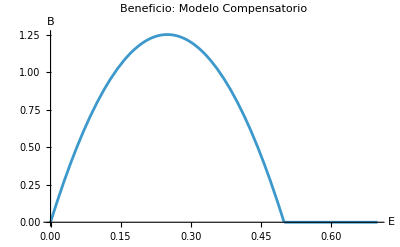

```mathematica
(*Definimos el modelo y parámetros*)r=0.5;K=10;q=1;
Fcomp[x_]:=r*x*(1-x/K);

(*Esfuerzo crítico E* *)
EstarComp=(D[Fcomp[x],x]/. x->0)/q; (*Da 0.5*)

(*Equilibrio estable x2 para E<E* *)
x2Comp[e_]:=K*(1-(q*e)/r);

(*Curva de beneficio*)
Bcomp[e_]:=If[e<EstarComp,q*e*x2Comp[e],0];

Plot[Bcomp[e],{e,0,0.7},PlotLabel->"Beneficio: Modelo Compensatorio",AxesLabel->{"E","B"}]
```

### Modelo Despensatorio

```mathematica
q=1;r=0.5;K=10;
(*Usamos una forma polinómica simple que sea convexa al inicio*)
fDesp[x_]:=r*(x^2/K)*(1-x/K);

(*Hallamos el esfuerzo máximo e**por tangencia*)
solTangencia=NSolve[{fDesp[x]==e*x,D[fDesp[x],x]==e,x>0},{x,e}][[4]];
estarStar=e/. solTangencia; (*Este es el valor de colapso*)

(*Función de beneficio B=q*e*x_estable*)
(*Buscamos el equilibrio x estable (el más grande)*)
xEstable[e_]:=Max[x/. NSolve[fDesp[x]==q*e*x,x]];
beneficio[e_]:=If[e<=estarStar,q*e*xEstable[e],0];

(*Representación de la curva esfuerzo-beneficio*)
Plot[beneficio[e],{e,0,estarStar*1.2},PlotRange->All,AxesLabel->{"e","B"},PlotLabel->"Curva Beneficio - Modelo Despensatorio",PlotStyle->Orange]
```

Part::partw: Part 4 of {{x→5.,e→0.125}} does not exist.

ReplaceAll::reps: {{{x→5.,e→0.125}}⟦4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value 1.2 (e/.{{x→5.,e→0.125}}⟦4⟧) in {e,0,1.2 (e/.{{x→5.,e→0.125}}⟦4⟧)} is not a machine-sized real number.

Plot[beneficio[e],{e,0,estarStar 1.2},PlotRange→All,AxesLabel→{e,B},PlotLabel→Curva Beneficio - Modelo Despensatorio,PlotStyle→Orange]

### Modelo Despensatorio Crítico

Aquí solo existe el valor crítico E**. La mayor diferencia es que, si la población se extingue por exceso de pesca, es irrecuperable aunque bajemos el esfuerzo, porque el origen es un equilibrio estable.

```mathematica
(*Parámetros:a=umbral crítico,K=soporte,r=tasa*)q=1;r=0.1;a=2;K=10;
fCrit[x_]:=r*x*(x/a-1)*(1-x/K);

(*Hallamos e**(punto donde la recta de pesca es tangente a la curva)*)
solCrit=NSolve[{fCrit[x]==e*x,D[fCrit[x],x]==e,x>a},{x,e}][[4]];
eMaxCrit=e/. solCrit;

(*Calculamos el beneficio para la rama superior estable*)
xEstableCrit[e_]:=Max[x/. NSolve[fCrit[x]==q*e*x,x]];
beneficioCrit[e_]:=If[e<=eMaxCrit,q*e*xEstableCrit[e],0];

(*Gráfica de la curva esfuerzo-beneficio*)
Plot[beneficioCrit[e],{e,0,eMaxCrit*1.2},PlotRange->All,AxesLabel->{"e","B"},PlotLabel->"Curva Beneficio - Modelo Despensatorio Crítico",PlotStyle->Red]
```

Part::partw: Part 4 of {{x→6.,e→0.08}} does not exist.

ReplaceAll::reps: {{{x→6.,e→0.08}}⟦4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value 1.2 (e/.{{x→6.,e→0.08}}⟦4⟧) in {e,0,1.2 (e/.{{x→6.,e→0.08}}⟦4⟧)} is not a machine-sized real number.

Plot[beneficioCrit[e],{e,0,eMaxCrit 1.2},PlotRange→All,AxesLabel→{e,B},PlotLabel→Curva Beneficio - Modelo Despensatorio Crítico,PlotStyle→Red]

## Ejercicio 3.11

```mathematica
Modelo Compensatorio
```

Modelo Compensatorio

```mathematica
Manipulate[Module[{f,h,xeq,b},f[x_]:=0.5*x*(1-x/10);
h[x_]:=e*x;
(*Calculamos el equilibrio estable*)xeq=Max[0,10*(1-e/0.5)];
b=e*xeq;
GraphicsRow[{(*Gráfica 1:Tasa de crecimiento y Pesca*)Plot[{f[x],h[x]},{x,0,12},PlotRange->{0,1.5},AxesLabel->{"x","F(x)"},PlotLabel->"Puntos de Equilibrio",Epilog->{Red,PointSize[Large],Point[{xeq,e*xeq}]}],(*Gráfica 2:Curva Esfuerzo-Beneficio*)Plot[e2*Max[0,10*(1-e2/0.5)],{e2,0,0.6},AxesLabel->{"e","B"},PlotLabel->"Beneficio",Epilog->{Red,PointSize[Large],Point[{e,b}]}]},ImageSize->700]],{{e,0.1,"Esfuerzo (e)"},0,0.6}]
```

### Modelo Despensatorio

```mathematica
Manipulate[Module[{f,h,sols,xeq,b},f[x_]:=0.08*x^2*(1-x/10);
h[x_]:=e*x;
(*Buscamos equilibrios positivos*)sols=x/. NSolve[f[x]==e*x&&x>0,x];
xeq=If[sols=={},0,Max[sols]];
b=e*xeq;
GraphicsRow[{Plot[{f[x],h[x]},{x,0,12},PlotRange->{0,0.8},AxesLabel->{"x","F(x)"},Epilog->{Orange,PointSize[Large],Point[{xeq,e*xeq}]}],(*Beneficio con rama de colapso*)Plot[ee*Max[0,x/. NSolve[f[x]==ee*x&&x>0,x]/. {}->{0}],{ee,0,0.25},AxesLabel->{"e","B"},Epilog->{Orange,PointSize[Large],Point[{e,b}]}]},ImageSize->700]],{{e,0.05,"Esfuerzo (e)"},0,0.25}]
```

### Modelo Despensatorio .08Crítico

```mathematica
Manipulate[Module[{f,h,sols,xeq,b},f[x_]:=0.1*x*(x/2-1)*(1-x/10);
h[x_]:=e*x;
sols=x/. NSolve[f[x]==e*x&&x>2,x];
xeq=If[sols=={},0,Max[sols]];
b=e*xeq;
GraphicsRow[{Plot[{f[x],h[x]},{x,0,12},PlotRange->{-0.5,1},AxesLabel->{"x","F(x)"},Epilog->{Red,PointSize[Large],Point[{xeq,e*xeq}]}],Plot[ee*Max[0,x/. NSolve[f[x]==ee*x&&x>2,x]/. {}->{0}],{ee,0,0.15},AxesLabel->{"e","B"},Epilog->{Red,PointSize[Large],Point[{e,b}]}]},ImageSize->700]],{{e,0.02,"Esfuerzo (e)"},0,0.15}]
```

## Ejercicio 3.12

```mathematica
ludwig[x_,r_,K_,a_, b_]:=r*x*(1-(x/K))-((b*x^2)/a^2 + x^2)

Manipulate[Plot[ludwig[x, r, K, a, b],{x,0,20},PlotRange->All,PlotStyle->{Thick,Blue},AxesLabel->{"u","x(t)"},PlotLabel->Style["Modelo de Ludwig",Bold,14],Filling->Axis], {r, 1, 10}, {K, -10, 10}, {a, -10, 10}, {b, -10, 10}]
```

```mathematica
ludwigadim[u_,q_,s_]:=u(1-q*u)-s*((u^2) / (1 + u^2))

Manipulate[Plot[ludwigadim[u, q, s],{u,0,20},PlotRange->All,PlotStyle->{Thick,Blue},AxesLabel->{"u","x(t)"},PlotLabel->Style["Modelo de Ludwig (adimensionado)",Bold,14],Filling->Axis],

{{q,0},-0.1,0.1,Appearance->"Labeled"},{{s,1},-10,10,Appearance->"Labeled"}]
```

## Ejercicio 3.13

Para determinar los puntos de equilibrio, debemos hallar los puntos de corte entre las dos funciones ; es decir, hallar los  tales que .
Primero, tenemos que , esto es, . Desarrollamos para obtener el polinomio de tercer grado: . Los puntos de equilibrio vienen dados por la solución analítica a la ecuación.
Ahora, para determinar un par  para el cual existen dos puntos de equilibrio, fijamos . Sabemos que las gráficas deben de ser tangentes, además de cortarse.
Calculamos las derivadas respecto a :

,
.

```mathematica
qParam[c_]:=(2 c^3)/(c^2-1)
sParam[c_]:=(2 c^3)/(1+c^2)^2

(*1. Buscamos los valores de c para q=7*)
cSol=NSolve[{qParam[c]==7,c>1},c];

(*2. Calculamos los valores críticos de s para esos c*)
sCriticos=sParam[c]/. cSol
(*Salen s1≈0.513 y s2≈0.601*)
```

{0.593851,0.524355}

```mathematica
(*Caso 4 equilibrios (3 positivos+el cero)*)q=7;s=0.55;
NSolve[u (s (1-u/q)-u/(1+u^2))==0&&u>=0,u]

(*Caso 3 equilibrios (Tangencia)*)
q=7;s=0.51307;
NSolve[u (s (1-u/q)-u/(1+u^2))==0&&u>=0,u]

(*Caso 2 equilibrios (1 positivo+el cero)*)
q=7;s=0.4;
NSolve[u (s (1-u/q)-u/(1+u^2))==0&&u>=0,u]
```

{{u→0.},{u→0.796903},{u→2.18744},{u→4.01566}}

{{u→0.},{u→0.674628}}

{{u→0.},{u→0.450107}}

## Ejercicio 3.14

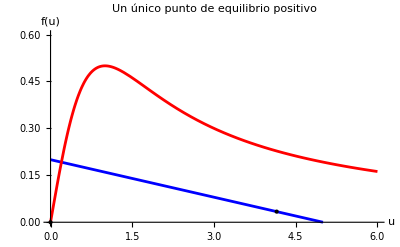

```mathematica
(*Caso 1:Un solo equilibrio estable*)q=5;s=0.2;
alpha[u_]:=s*(1-u/q);
beta[u_]:=u/(1+u^2);

Plot[{alpha[u],beta[u]},{u,0,6},PlotStyle->{Blue,Red},PlotRange->{0,0.6},PlotLabel->"Un único punto de equilibrio positivo",AxesLabel->{"u","f(u)"},Epilog->{PointSize[Large],Black,Point[{0,0}],(*Inestable*)Point[{4.15,alpha[4.15]}],(*Estable u1*)Arrow[{{1,-0.05},{2,-0.05}}],(*Crece hacia u1*)Arrow[{{6,-0.05},{5,-0.05}}] (*Decrece hacia u1*)}]
```

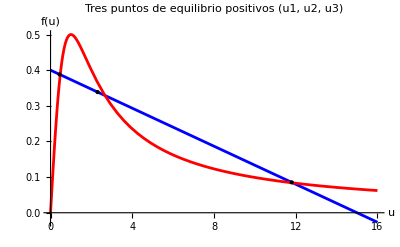

```mathematica
(*Caso 2:Tres equilibrios positivos*)q=15;s=0.4;
Plot[{alpha[u],beta[u]},{u,0,16},PlotStyle->{Blue,Red},PlotLabel->"Tres puntos de equilibrio positivos (u1, u2, u3)",AxesLabel->{"u","f(u)"},Epilog->{PointSize[Medium],Point[{0.45,alpha[0.45]}],(*u1 Estable*)Point[{2.3,alpha[2.3]}],(*u2 Inestable*)Point[{11.8,alpha[11.8]}],(*u3 Estable*)(*Comportamiento en el eje*)Arrow[{{0.1,-0.05},{0.3,-0.05}}],(*Hacia u1*)Arrow[{{1,-0.05},{0.7,-0.05}}],(*Hacia u1*)Arrow[{{4,-0.05},{6,-0.05}}],(*Hacia u3*)Arrow[{{15,-0.05},{13,-0.05}}]    (*Hacia u3*)}]
```

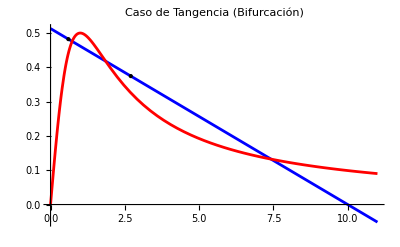

```mathematica
(*Caso 3:Tangencia (Puntos de bifurcación)*)q=10;s=0.513; (*Valores aproximados para tangencia*)
Plot[{alpha[u],beta[u]},{u,0,11},PlotStyle->{Blue,Red},PlotLabel->"Caso de Tangencia (Bifurcación)",Epilog->{PointSize[Large],Point[{0.6,alpha[0.6]}],(*u1 estable*)Point[{2.7,alpha[2.7]}]  (*u2 punto de tangencia*)}]
```

## Ejercicio 3.15

```mathematica
alpha[u_,q_,s_]:=s(1-u/q)
beta[u_]:=u / (1 + u^2)
Manipulate[Plot[{alpha[u,q,s],beta[u]},{u,0,10},PlotRange->All,PlotLabel->Column[{Row[{"Alpha y beta"}]},Alignment->Center],AxesLabel->{"x","f(x)"}
],
{{q,7},0.1,10,Appearance->"Labeled"},{{s,0.5},0,1,Appearance->"Labeled"}]
```

## Ejercicio 3.16

```mathematica
Clear[c,q,s,u]
```

Vamos a localizar el punto singular (cúspide) del espacio de parámetros y el punto de inflexión de la función de depredación β(u).
La curva de bifurcación, que marca los puntos donde el modelo de Ludwig tiene equilibrios por tangencia, está parametrizada por c>1 como


Para hallar la cúspide P=(), debemos encontrar el valor de c que anula las primeras derivadas de ambas funciones.

```mathematica
(*Definimos las funciones de la curva de tangencia*)
q[c_]:=(2*c^3)/(c^2-1)
s[c_]:=(2*c^3)/(1+c^2)^2

(*1. Hallamos el valor de c para el punto de cúspide*)
(*Resolvemos dq/dc=0 para c>1*)
solC=Solve[D[q[c],c]==0&&c>1,c];
valorC=c/. solC; (*Esto nos devuelve Sqrt[3]*)

(*Calculamos las coordenadas del punto P*)
puntoP={q[valorC],s[valorC]}//Simplify
(*El resultado es {3*Sqrt[3],(3*Sqrt[3])/8}*)

(*2. Calculamos el punto de inflexión de beta(u)*)
beta[u_]:=u/(1+u^2)
segundaDer=D[beta[u],{u,2}];
puntoInflexion=Solve[segundaDer==0&&u>0,u]
(*El resultado es u->Sqrt[3]*)
```

{{3 √3},{(3 √3)/8}}

{{u→√3}}

## Ejercicio 3.17

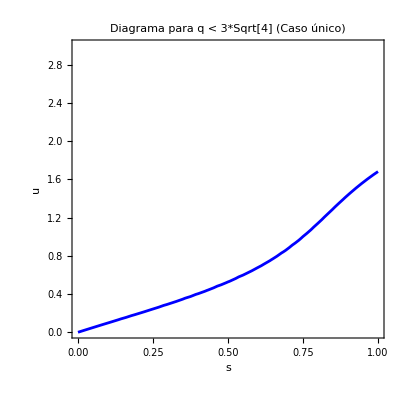

```mathematica
q1 = 3; (* Un valor menor que 5.196 *)
ContourPlot[s*(1 - u/q1) == u/(1 + u^2), {s, 0, 1}, {u, 0, q1},
 FrameLabel -> {"s", "u"},
 PlotLabel -> "Diagrama para q < 3*Sqrt[4] (Caso único)",
 ContourStyle -> Blue]
```

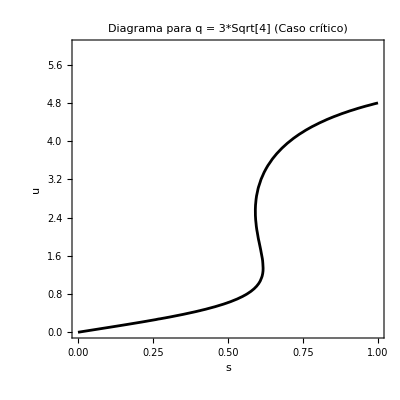

```mathematica
qcrit=3*Sqrt[4];
ContourPlot[s*(1-u/qcrit)==u/(1+u^2),{s,0,1},{u,0,qcrit},FrameLabel->{"s","u"},PlotLabel->"Diagrama para q = 3*Sqrt[4] (Caso crítico)",ContourStyle->Black]
```

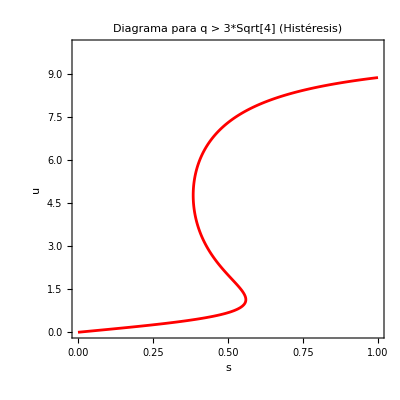

```mathematica
q3=10; (*Un valor mayor que 5.196*)
ContourPlot[s*(1-u/q3)==u/(1+u^2),{s,0,1},{u,0,q3},FrameLabel->{"s","u"},PlotLabel->"Diagrama para q > 3*Sqrt[4] (Histéresis)",ContourStyle->Red,PlotPoints->100]
```

## Ejercicio 3.18

```mathematica
Manipulate[ContourPlot[s*(1-u/q)-u/(1+u^2)==0,{s,0,1},{u,0,q},FrameLabel->{"Parámetro s","Equilibrio u"},PlotLabel->Style[Row[{"Diagrama de bifurcación plano (q = ",q,")"}],12],ContourStyle->{Blue,Thickness[0.005]},GridLines->Automatic,PlotPoints->60,Exclusions->None],{{q,10,"Parámetro q"},2,20,Appearance->"Labeled"}]
```

## Ejercicios relación

## 4.

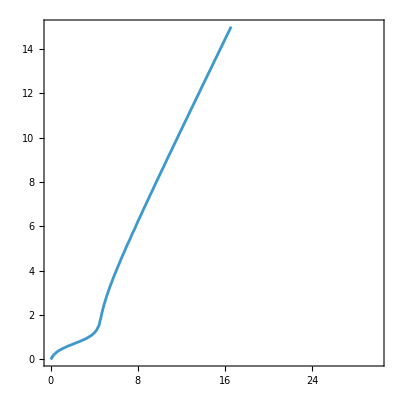

```mathematica
ContourPlot[alpha[u,q,0.7]==beta[u],{q,0,30},{u,0,15}]
```

## 10.

```mathematica
alpha1[x_,a_,b_]:=(1+a(x+1))
beta1[x_,a_,b_]:=(b x)/(x+1)
Manipulate[Plot[{alpha1[x,a,b],beta1[x,a,b]},{x,0,10},PlotRange->All,PlotLabel->Column[{Row[{"Alpha y beta"}]},Alignment->Center],AxesLabel->{"x","f(x)"}
],
{{a,0.1},0,10,Appearance->"Labeled"},{{b,0.5},0,10,Appearance->"Labeled"}]
```